# HyperBloch package tutorial

## Higher-order topology

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Higher-order topology tutorial on the HyperCells&HyperBloch website.  In this tutorial we will see how to construct an elementary nearest-neighbor hopping model with multiple orbitals per site for (supercell) model graphs  (constructed through HyperBloch’s sister package HyperCells). This will enable us to set up a variant of the Benalcazar-Bernevig-Hughes model, BBH model. Moreover, we will demonstrate the bulk-boundary correspondence by analyzing spectra computed for finite flakes with open boundary conditions, where we will see how disclination defects can be introduced in finite sized system.

## Preliminaries:

### Remarks:

Before using the notebook to the Higher-order topology tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc
{6,4}-tess-NN_T2.2_3.hcm
{6,4}-tess-NN_T2.2_3_sc-T5.4.hcs
{6,4}-tess-NN_T2.2_3_sc-T9.3.hcs

In case no such files exist in your current directory, please follow the instructions in the  HyperBloch Higher-order topology tutorial, or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Needed functions:

In previous tutorials, such as getting started with the HyperBloch package and HyperBloch Supercells tutorial etc., we have calculated the density of states of various tight-binding models via exact diagonalization and random samples. We predefine a function in order to calculate the eigenvalues for the Abelian Bloch Hamiltonians that we will construct. We  take advantage of the independence of different momentum sectors and parallelize the computation, where we partition the set of Npts into  Nruns subsets:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

## (Supercell) model graphs:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

where we consider the unit cell T2.2 as the primitive cell.

### Import (supercell) model graphs:

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NN_T2.2_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{6,4}-tess-NN_T2.2_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

For convenience, let us collect the (supercell) model graphs in one Association:

```mathematica
cmodels=Join[Association[cells[[1]]->pcmodel], scmodels];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst= Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Visualize model graph:

We can visualize the model graph with the high-level visualization function VisualizeModelGraph:

```mathematica
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
NumberOfGenerations->3,
Elements-><|
	ShowCellGraphFlattened->{},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->300]
```

-Graphics-

## Multiple orbitals per site:

Every (supercell) model graph can be equipped with multiple orbitals per site, and even with a varying number of orbitals at each site. It is instructive to start with an elementary nearest-neighbor hopping model in order to get familiar with the procedures to assign coupling constants.  We will use these guiding principles to construct the {6,4}-BBH model in the subsequent section.

### Construct Hamiltonians:

#### Orbitals:

The first step to construct such models consists of specifying the number of orbitals at each site. 
We will set the number of orbitals per site to four:

```mathematica
Norb=4;
```

Correspondingly, the coupling constants need to be adjusted appropriately such that every orbital is coupled to intra- and inter-site orbitals as desired.

#### On-site terms:

Intra-site mass:

Imagine placing a set of four orbitals, numbered from 1 to 4, uniformly around each vertex in the model graph. The on-site terms for the individual orbitals are constructed by specifying a 4×4  identity matrix for each vertex, which we choose to set to zero:

```mathematica
onsiteMassMat=0{
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}};
```

Intra-site  interactions :

By choosing the assigned numbers of the orbitals to increase in counter-clockwise direction around a vertex, we are able to define a undirected cycle of intra-site hopping terms. These hopping amplitudes can be defined at the level of the vertex on-site terms as well, through the corresponding matrix:

```mathematica
onsiteInteractionMat={
{0,1,0,1},
{ 1,0,1,0},
{0,1,0,1},
{1,0,1,0}};
```

For example, the first row in the matrix onsiteMat describes the hopping amplitudes of orbital 1, which couples with orbitals 2 and 4. 
These coupling constants can be assigned by associating the amplitudes with vertices in the model graph:

```mathematica
vertices=VertexList@pcmodel["Graph"];
onsitePC=AssociationThread[vertices->ConstantArray[onsiteMassMat + onsiteInteractionMat,Length@vertices]];
```

#### (Inter-site) hopping terms:

Assigning  the  appropriate  hopping  amplitudes  relies  on  the  identification  of  the  set  of  directed  edges  connecting  vertices  in  the  model  graph  of  the  primitive  cell. The needed information can be extracted by printing the list of edges in the model graph:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{{1,1},1,7}},{2,3}{2,1}{1,{{1,2},6,12}},{2,1}{2,3}{1,{{1,3},13,23}},{2,2}{2,4}{1,{{1,4},2,8}},{2,4}{2,2}{1,{{1,5},15,19}},{2,2}{2,1}{1,{{1,6},14,24}},{2,5}{2,3}{1,{{1,7},5,11}},{2,3}{2,5}{1,{{1,8},18,22}},{2,4}{2,6}{1,{{1,9},3,9}},{2,6}{2,4}{1,{{1,10},16,20}},{2,6}{2,5}{1,{{1,11},4,10}},{2,5}{2,6}{1,{{1,12},17,21}}}

A careful inspection of the individual edges reveals that we need two matrices to describe the inter-site hopping amplitudes, one for intra-cell coupling terms and one for inter-cell couplings.

Intra-cell:

The intra-cell hopping amplitudes couple the orbitals 1 and 1 as well as 2 and 4 of different vertices in the same unit cell, as such, the corresponding matrix is given by:

```mathematica
hopIntraCellMat={
{1,0,0,0},
{0,0,0,1},
{0,0,0,0},
{0,0,0,0}};
```

Inter-cell:

The inter-cell hopping amplitudes couple the orbitals 2 and 4 as well as 3 and 3 of different vertices in an adjacent copy of the unit cell, as such, the corresponding matrix is given by:

```mathematica
hopInterCellMat={
{0,0,0,0},
{0,0,0,1},
{0,0,1,0},
{0,0,0,0}};
```

The intra and inter-cell hopping amplitudes can be assigned by inspecting the list of edges in the model graph. To make sure that we assign the hopping amplitudes correctly, we can take a look at the translation operators associated with the edges (see also getting started with the HyperBloch package):

```mathematica
pcmodel["EdgeTranslations"]
```

{1,1,g1,1,g3,g2,1,g4^-1*g2^-1,1,g4,1,g3^-1*g1^-1}

Edges associated with trivial translations should be endowed with intra-cell hopping amplitudes and inter-cell hopping amplitudes otherwise. The coupling constants can be assigned by inspection, or programmatically:

```mathematica
hoppingsVec=If[#=="1", hopIntraCellMat, hopInterCellMat]&/@pcmodel["EdgeTranslations"];
```

These coupling constants can be assigned by associating the amplitudes with edges in the model graph:

```mathematica
edges=EdgeList@pcmodel["Graph"];
hoppingsPC=AssociationThread[edges->hoppingsVec];
```

#### Hamiltonians:

Once the (supercell) model graphs are imported and the coupling constants are assigned the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,Norb&,onsitePC,hoppingsPC,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],Norb&,onsitePC,hoppingsPC,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  10^3 random samples in momentum space and 12 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#], 10^3,12,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.02, (this might take a minute):

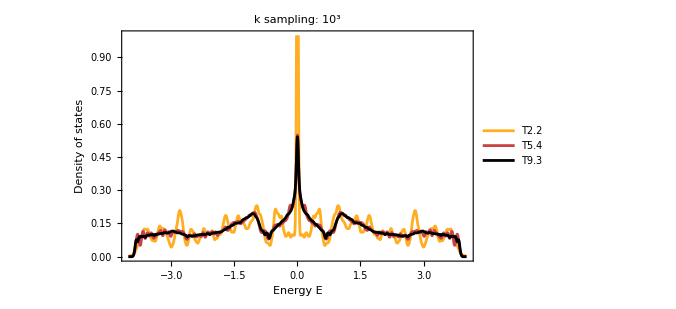

```mathematica
SmoothHistogram[evals,0.02,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
LabelStyle->20,ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},
PlotLabel->"k sampling: 10^3",PlotRange->{0, 1},PlotStyle->cLst]
```

## {6,4}-BBH model

The {6,4}-BBH model can be constructed by tweaking some of the hopping amplitudes we have previously set up. This, in effect, will enable us to thread the {6,4}-lattice with magnetic π-fluxes in certain regions. Concretely, our goal is to thread the lattice with π-fluxes through each cycle of orbitals and each plaquette with alternating inter- and intra-site hopping amplitudes.

### Constructing Hamiltonians:

#### On-site terms:

The on-site terms can be used to introduce π-fluxes through each cycle of orbitals. We choose to adjust the intra-site coupling between orbital 1 and 4 by changing the sign of the hopping amplitude in the on-site terms:

```mathematica
onsiteInteractionMat=h0{
{   0,   1,   0,-1},
{   1,   0,   1,   0},
{   0,   1,   0,   1},
{ -1,   0,  1,   0}};
```

where we have introduced a coupling constant h0 in order tune the intra-site coupling strength.
We assign the coupling constants through the following Association:

```mathematica
vertices=VertexList@pcmodel["Graph"];
onsitePC=AssociationThread[vertices->ConstantArray[onsiteInteractionMat,Length@vertices]];
```

#### (Inter-site) hopping terms:

The on-site terms also introduce π-fluxes through some plaquettes with alternating inter- and intra-site hopping amplitudes. Therefore, we need to perform yet another modification such that every such plaquette is threaded by a π-flux. The hopping amplitudes can be used to introduce the corresponding magnetic fluxes. We choose to adjust the inter-site coupling between orbital 3 and 3 of another site by changing the sign of the inter-cell hopping amplitudes:

```mathematica
hopInterCellMat={
{   0,   0,   0,  0},
{   0,   0,   0,  1},
{   0,   0,-1,  0},
{   0,   0,   0,  0}};
```

```mathematica
hoppingsVec=h1 If[#=="1",hopIntraCellMat, hopInterCellMat]&/@pcmodel["EdgeTranslations"];
```

where we have introduced a coupling constant h1 in order tune the inter-site coupling strength. Therefore:

```mathematica
edges=EdgeList@pcmodel["Graph"];
hoppingsPC=AssociationThread[edges->hoppingsVec];
```

#### Hamiltonians:

Once the (supercell) model graphs are imported and the coupling constants are assigned the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,Norb&,onsitePC,hoppingsPC,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],Norb&,onsitePC,hoppingsPC,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

Three distinct phases can be identified by tuning the parameters. 
For brevity, let us use Associations to collect the data sets we want to visualize:

```mathematica
phases={"Topological phase", "Metallic phase","Trivial phase"};
h0Lst=AssociationThread[phases,{0.5,0.77,1.5}];
```

We compute the Eigenvalues with a set of  10^3 random samples in momentum space and 8 subsets, (this might take a minute):

```mathematica
evals=Association[
Table[phase->
Association[#->ComputeEigenvalues[Hclst[#]/.{h0->h0Lst[phase],h1->1},  10^3,8,genusLst[#]]&/@cells],
{phase,phases}]
];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.02, (this might take a minute):

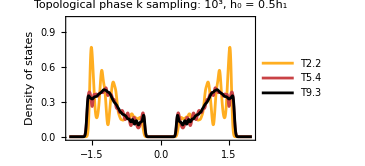
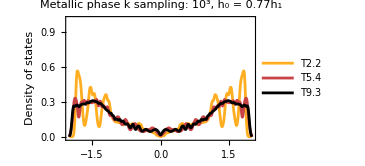
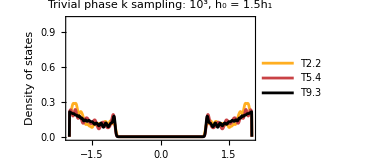

```mathematica
Row[
SmoothHistogram[evals[#],0.02,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->270,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->15,
PlotLabel-># <>"\nk sampling: 10^3, h_0 = "<>ToString@h0Lst[#] <>"h_1",
PlotRange->{{-2,2},{-0.01,1.01}},PlotStyle->cLst]&/@phases,
FrameMargins->0,ImageMargins->0]
```

Note that at the gap closing  h_0=0.77h_1, the transition for small supercells appears semi-metallic with vanishing density of states at E = 0. However,  the DOS converges to a finite value for larger supercells, which implies that this is a finite-size effect.

## Finite flakes

Our next goal is to demonstrate the bulk-boundary correspondence in the higher-order topological phase of the {6,4}-BBH model. We can repurpose the constructed sequence of (supercell) model graphs in order to analyse the spectrum for finite flakes with open boundary conditions.

### Visualize finite flakes:

Before we terminate the system to a finite size, let us visualize the flakes we want to consider. This can be achieved by turning off the display of inter-cell edges specified through the option ShowInterCellEdges of the function ShowCellGraphFlattened within the function VisualizeModelGraph by setting it to False:

```mathematica
regularFlakes=Row[
VisualizeModelGraph[cmodels[#],
LabelStyle->20,NumberOfGenerations->3,PlotLabel->#,
Elements -> <|
	ShowCellGraphFlattened -> {
	ShowVertexLabels->False,
	ShowInterCellEdges->False}
|>,
ImageSize->300]
&/@cells]
```

-Graphics--Graphics--Graphics-

### Hamiltonians for finite flakes:

We can reuse the assigned coupling constants for the {6,4}-BBH model in the bulk without adjustments.  The tight-binding Hamiltonians for finite flakes in real space can be constructed through the function TBClusterHamiltonian, which take the same arguments as the  AbelianBlochHamiltonian function:

```mathematica
HcFlakelst =Join[
Association[cells[[1]]-> TBClusterHamiltonian[pcmodel,Norb&,onsitePC,hoppingsPC]],
Association[#-> TBClusterHamiltonian[scmodels[#],Norb&,onsitePC,hoppingsPC, PCModel->pcmodel]&/@cells[[2;;]]]
];
```

### Energy spectrum:

We can compute the spectra for the {6,4}-BBH models on finite flakes with open boundary conditions as follows:

```mathematica
evals=Association[#->Eigenvalues[HcFlakelst[#]/.{h0->0.1,h1->1}]&/@cells];
```

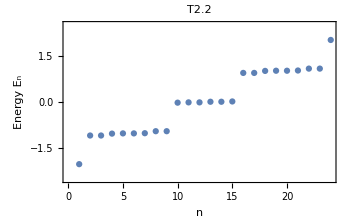
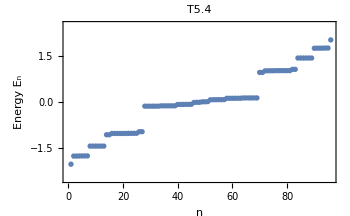
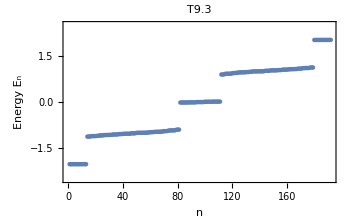

```mathematica
Row[
ListPlot[Sort[evals[#]],
AxesOrigin->{0,-2.5},Frame->True,
FrameLabel->{"n","Energy E_n"},FrameStyle->Black,
ImageSize->350,LabelStyle->20,PlotLabel->#,
PlotRange->{Automatic, {-2.5,2.5}}]&/@cells
]
```

The emergence of gaps implies the existence of boundary modes in the topological phase.

## Disclination defects:

The introduction of disclination defects enables us to demonstrate the existence of boundary modes and associated quantized fractional charges in higher-order topological insulators. The HyperBloch package provides a function for the construction of finite flakes with disclination defects. This is achieved through a cutting and gluing procedure known as the Volterra process.

### Introduce a disclination defect:

We choose to introduce a disclination defect by cutting away a sector in the finite flake subtended by an angle π/3, and glue the newly introduced borders together. The disclination defect can easily be introduced in .08(supercell) model graphs through the function IntroduceDisclinationInModelGraph. Aside from the (supercell) model graphs, two arguments need to be passed to the function:

FrankAngleIncrement Δα_F:

The Frank angle specifies the angle of the empty region introduced in the finite flake before the borders are glued together.  It can be specified through an integer which we denote as the FrankAngleIncrement Δα_F. The actual Frank angle is then given by α_F=Δα_F 2π/m, where m is given by the C_m rotation symmetry m∈ {r, q, p}  specified by the chosen cell center. In our case m=6.

We want to set α_F to -π/3, where the negative sign indicates that the empty region is introduced through cutting away a sector subtended by α_F.  As such, we set the FrankAngleIncrement to Δα_F=-1.

ReferenceAngleIncrement Δα_R:

A reference angle α_R needs to be passed, which specifies the relative rotation angle in counter-clockwise direction of the normal vector to a reference vector v⃗={1,0}, defining the disclination defect. Analogous to the FrankAngleIncrement Δα_F, the reference angle is specified by a positive integer, which we denote as the ReferenceAngleIncrement Δα_R. The actual reference angle is then given by α_R=Δα_R π/m.

We choose a zero reference angle, as such, we set the ReferenceAngleIncrement to  Δα_R=0.

```mathematica
cmodelsDisclination = Association[#->IntroduceDisclinationInModelGraph[cmodels[#], -1,0]&/@cells];
```

### Visualize finite flakes with disclinations:

(Supercell) model graphs with disclination defects can be visualized as regular (supercell) model graphs:

```mathematica
Row[
VisualizeModelGraph[cmodelsDisclination[#],
LabelStyle->20,PlotLabel->#,
NumberOfGenerations->3,
Elements -> <|
	ShowCellGraphFlattened -> {ShowVertexLabels->False}
|>, 
ImageSize->300]
&/@cells]
```

-Graphics--Graphics--Graphics-

### Details:

#### Glued edges:

The newly introduced edges can be accessed through the key “GluedEdges”. They inherit some of the labels originating from the (supercell) model graphs they are based on. Each glued edge carries an edge tag containing a list of the form { “g”, idx } where the string “g” indicates that the edge is a glued edge and  idx is a running index, indicating the position in the list of glued edges.

For example, for the model graph based on the T2.2 primitive cell the glued edges are:

```mathematica
cmodelsDisclination["T2.2"]["GluedEdges"]
```

{{2,3}{2,2}{1,{{g,1},6,7}}}

and for the supercell model graph based on the T5.4 supercell the glued edges are:

```mathematica
cmodelsDisclination["T5.4"]["GluedEdges"]
```

{{2,3,1}{2,2,1}{3,2,{1,{{g,1},6,7}}}}

Let us highlight the glued edges by using the EdgeFilter option in the function ShowCellGraphFlattened within the function VisualizeModelGraph as follows:

```mathematica
disclinationFlakes=Row[
Table[
Show[
VisualizeModelGraph[cmodelsDisclination[cell],
PlotLabel->cell,LabelStyle->20,
NumberOfGenerations->3,
Elements -> <|
	ShowCellGraphFlattened -> {
	ShowVertexLabels->False ,
	EdgeFilter->(MemberQ[cmodelsDisclination[cell]["GluedEdges"],#]==False&)}
|>,
ImageSize->300],

ShowCellGraphFlattened[cmodelsDisclination[cell],
EdgeFilter->(MemberQ[cmodelsDisclination[cell]["GluedEdges"],#]&),
IntraCellEdgeStyle->Directive[Green,AbsolutePointSize[3]],
ShowVertexLabels->False]
],{cell,cells}]
]
```

-Graphics--Graphics--Graphics-

#### Symmetrized flakes (bonus):

(Supercell) model graphs with disclination defects can be represented in a symmetrized form by specifying the option SymmetrizeFlake in the function IntroduceDisclinationInModelGraph:

```mathematica
cmodelsDisclinationSymmetric=Association[#->IntroduceDisclinationInModelGraph[cmodels[#],-1,0,SymmetrizeFlake->True]&/@cells];
```

The disclination defect can be indicated with the option IndicateDisclination in the function VisualizeModelGraph if the (supercell) model graphs with a disclination defect is  symmetrized:

```mathematica
disclinationFlakesSymmetrized=Row[
VisualizeModelGraph[cmodelsDisclinationSymmetric[#],
DisclinationLineStyle->Directive[Red,Dashed,AbsoluteThickness[1.5]],
IndicateDisclination->True,
LabelStyle->20,PlotLabel->#,
NumberOfGenerations->3,
Elements -> <|
	ShowCellGraphFlattened -> {ShowVertexLabels->False}
|>, 
ImageSize->300]
&/@cells]
```

-Graphics--Graphics--Graphics-

#### Visualize the Volterra process (bonus):

The Volterra process can be visualized step by step. For example, let us consider the T9.3 supercell.

We have already set up all needed graphs, the only missing ingredients are the two lines indicating the cut out wedge. They can easily be constructed by extracting the Frank angle and the reference angle:

```mathematica
FrankAngle=cmodelsDisclination["T9.3"]["FrankAngle"];
referenceAngle=cmodelsDisclination["T9.3"]["ReferenceAngle"];
```

The cut out sector subtended by an angle π/3 lies within the region specified by the following two lines:

```mathematica
upperCut=Line[{{0,0}, RotationMatrix[referenceAngle].RotationMatrix[Abs[FrankAngle/2]].{1,0}}];
bottomCut=Line[{{0,0}, RotationMatrix[referenceAngle].RotationMatrix[FrankAngle/2].{1,0}}];
```

The entire process can be visualized as follows:

```mathematica
Row[{
Show[regularFlakes[[1,3]],
Graphics[{Orange,Dashed,AbsoluteThickness[1.5],upperCut}],
Graphics[{Orange,Dashed,AbsoluteThickness[1.5],bottomCut}],
ImageSize->300,LabelStyle->20,PlotLabel->"Regular flake\n"],

Show[disclinationFlakes[[1,3]],ImageSize->300,LabelStyle->20,
PlotLabel->"Flake with a disclination\n"],

Show[disclinationFlakesSymmetrized[[1,3]],ImageSize->300,LabelStyle->20,
PlotLabel->"Flake with a disclination,\n symmetrized"]
}]
```

-Graphics--Graphics--Graphics-

### Hamiltonians for finite flakes with disclinations:

The construction of tight-binding Hamiltonians for finite flakes with a disclination defect is slightly more involved. The corresponding models graphs have glued edges that should be addressed individually when assigning coupling constants.

Primitive cell:

```mathematica
gluedEdges = cmodelsDisclination["T2.2"]["GluedEdges"];
hoppingsGlued=AssociationThread[gluedEdges->{hopIntraCellMat}];
```

```mathematica
HPCDisclinationFlake=TBDisclinationClusterHamiltonian[cmodelsDisclination["T2.2"], pcmodel,Norb&,onsitePC,hoppingsPC,hoppingsGlued];
```

1st supercell:

```mathematica
gluedEdges = cmodelsDisclination["T5.4"]["GluedEdges"];
hoppingsGlued=AssociationThread[gluedEdges->{hopIntraCellMat}];
```

```mathematica
HSC1DisclinationFlake=TBDisclinationClusterHamiltonian[cmodelsDisclination["T5.4"], pcmodel,Norb&,onsitePC,hoppingsPC,hoppingsGlued];
```

2nd supercell:

```mathematica
gluedEdges = cmodelsDisclination["T9.3"]["GluedEdges"];
hoppingsGlued=AssociationThread[gluedEdges->{hopIntraCellMat,hopInterCellMat}];
```

```mathematica
HSC2DisclinationFlake=TBDisclinationClusterHamiltonian[cmodelsDisclination["T9.3"], pcmodel,Norb&,onsitePC,hoppingsPC,hoppingsGlued];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
HcDisclinationFlakelst=AssociationThread[cells,{HPCDisclinationFlake,HSC1DisclinationFlake,HSC2DisclinationFlake}];
```

### Energy spectrum:

We can compute the spectra for the {6,4}-BBH models on finite flakes with a disclination defect and open boundary conditions as follows:

```mathematica
esys=Association[#->Eigenvalues[HcDisclinationFlakelst[#]/.{h0->0.1,h1->1}]&/@cells];
```

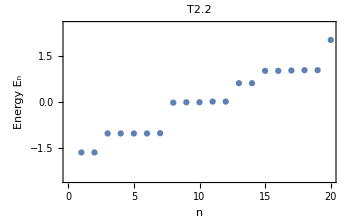
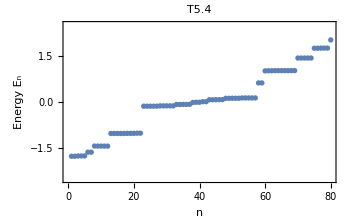
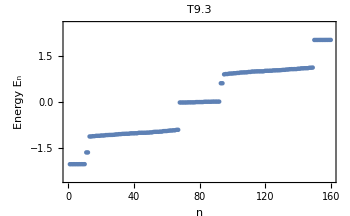

```mathematica
Row[
ListPlot[Sort[esys[#]],
AxesOrigin->{0,-2.5},Frame->True,
FrameLabel->{"n","Energy E_n"},FrameStyle->Black,
ImageSize->350,LabelStyle->20,PlotLabel->#,
PlotRange->{Automatic, {-2.5,2.5}}]&/@cells
]
```

We can compare the visualized spectra with the previous ones for the flakes without disclination defects. The emergence of the new in-gap states implies a filling anomaly and indicates quantized fractional charges.

Let us explicitly emphasize some of the in-gap states:

```mathematica
inGapStates=AssociationThread[cells,{{{12.5,14.5},{0.59,0.63}},{{57.5,59.5},{0.59,0.63}},{{92.5,94.5},{0.59,0.63}}}];
subPlotPosX=AssociationThread[cells,{{5,1.25},{20,1.25},{38,1.25}}];
```

```mathematica
Row[
ListPlot[Sort[esys[#]],
AxesOrigin->{0,-2.5},Frame->True,
FrameLabel->{"n","Energy E_n"},FrameStyle->Black,
ImageSize->350,LabelStyle->20,PlotLabel->#,
PlotRange->{Automatic, {-2.5,2.5}},

Epilog->Inset[
ListPlot[Sort[esys[#]],
Frame->True,ImageSize->Scaled[130],
PlotRange->inGapStates[#],
PlotStyle->Directive[Red,PointSize[Medium]]
],subPlotPosX[#]]
]&/@cells
]
```

-Graphics--Graphics--Graphics-

```mathematica
NotebookSave[]
```